```mathematica
response=Simplify[DSolve[{x''[t]==-2 ζ Subscript[ω, n] x'[t]-Subscript[ω, n]^2 x[t],x[0]==1,x'[0]==-1},x[t],t]]
```

{{x[t]→1/(2 √((-1+ζ^2) ω_n^2))ⅇ^(-t (ζ ω_n+√((-1+ζ^2) ω_n^2))) (1+(-1+ⅇ^(2 t √((-1+ζ^2) ω_n^2))) ζ ω_n+√((-1+ζ^2) ω_n^2)+ⅇ^(2 t √((-1+ζ^2) ω_n^2)) (-1+√((-1+ζ^2) ω_n^2)))}}

```mathematica
xSol=x[t]/.response[[1,1]]
```

ⅇ^(-t ζ ω_n) (Cosh[t √(-1+ζ^2) ω_n]+(Sinh[t √(-1+ζ^2) ω_n] (-1+ζ ω_n))/(√(-1+ζ^2) ω_n))

```mathematica
dxSol=FullSimplify[D[xSol,t]]
```

ⅇ^(-t ζ ω_n) (-Cosh[t √(-1+ζ^2) ω_n]+(Sinh[t √(-1+ζ^2) ω_n] (ζ-ω_n))/(√(-1+ζ^2)))

```mathematica
xSol1=xSol/.{Subscript[ω, n]->1.1892,ζ->0.5685}
```

ⅇ^(-0.67606 t) (Cos[(0.978335+0. ⅈ) t]-(0.331113+0. ⅈ) Sin[(0.978335+0. ⅈ) t])

```mathematica
dxSol1=dxSol/.{Subscript[ω, n]->1.1892,ζ->0.5685}
```

ⅇ^(-0.67606 t) (-Cos[(0.978335+0. ⅈ) t]-(0.754482+0. ⅈ) Sin[(0.978335+0. ⅈ) t])

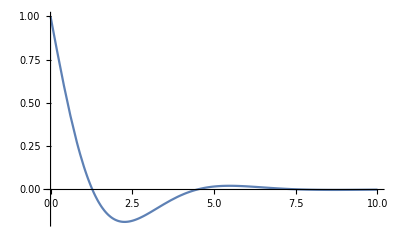

```mathematica
Plot[xSol1,{t,0,10},PlotRange->Full]
```

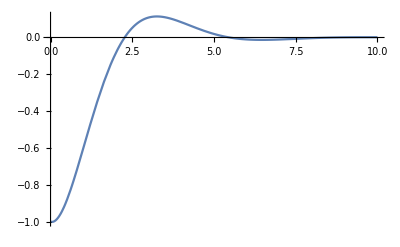

```mathematica
Plot[dxSol1,{t,0,10},PlotRange->Full]
```

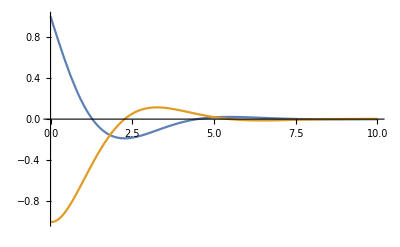

```mathematica
Plot[{xSol1,dxSol1},{t,0,10},PlotRange->Full]
```

```mathematica
(* State space repesentation of the given second order system *)
aMat={{0,1},{-1,0}};
bVec={{0},{1}};
```

```mathematica
(* Riccatti Equation *)
rMat={{r11,r12},{r12,r22}};
qMat={{q1,0},{0,q2}};
```

```mathematica
(* Closed-Loop Response of the System *)
cl=λ IdentityMatrix[2]-aMat+(1/p)bVec.Transpose[bVec].rMat;
MatrixForm[cl]
```

(λ | -1
1+r12/p | r22/p+λ)

```mathematica
detcl=Det[cl]
```

1+r12/p+(r22 λ)/p+λ^2

```mathematica
coeff=CoefficientList[detcl,λ]
```

{1+r12/p,r22/p,1}

```mathematica
r12Sol=Solve[coeff[[1]]==Subscript[ω, n]^2,r12]
```

{{r12→p (-1+ω_n^2)}}

```mathematica
r22Sol=Solve[coeff[[2]]==2 ζ Subscript[ω, n],r22]
```

{{r22→2 p ζ ω_n}}

```mathematica
RiccattiEqGeneral=qMat-(1/p)rMat.bVec.Transpose[bVec].rMat+rMat.aMat+Transpose[aMat].rMat;
MatrixForm[RiccattiEqGeneral]
```

(q1-2 r12-r12^2/p | r11-r22-(r12 r22)/p
r11-r22-(r12 r22)/p | q2+2 r12-r22^2/p)

```mathematica
RicMSD=RiccattiEqGeneral/.{r12Sol[[1,1]],r22Sol[[1,1]]};
MatrixForm[RicMSD]
```

(q1-2 p (-1+ω_n^2)-p (-1+ω_n^2)^2 | r11-2 p ζ ω_n-2 p ζ ω_n (-1+ω_n^2)
r11-2 p ζ ω_n-2 p ζ ω_n (-1+ω_n^2) | q2-4 p ζ^2 ω_n^2+2 p (-1+ω_n^2))

```mathematica
r11Sol=Solve[RicMSD[[1,2]]==0,r11]
```

{{r11→2 p ζ ω_n^3}}

```mathematica
q1Sol=Solve[RicMSD[[1,1]]==0,q1]
```

{{q1→-p+p ω_n^4}}

```mathematica
q2Sol=Solve[RicMSD[[2,2]]==0,q2]
```

{{q2→2 (p-p ω_n^2+2 p ζ^2 ω_n^2)}}

```mathematica
rNew=rMat/.{r11Sol[[1,1]],r12Sol[[1,1]],r22Sol[[1,1]]}
```

{{2 p ζ ω_n^3,p (-1+ω_n^2)},{p (-1+ω_n^2),2 p ζ ω_n}}

```mathematica
kTrn=(1/p)Transpose[bVec].rNew
```

{{-1+ω_n^2,2 ζ ω_n}}

```mathematica
xVec={{xSol},{dxSol}}
```

{{ⅇ^(-t ζ ω_n) (Cosh[t √(-1+ζ^2) ω_n]+(Sinh[t √(-1+ζ^2) ω_n] (-1+ζ ω_n))/(√(-1+ζ^2) ω_n))},{ⅇ^(-t ζ ω_n) (-Cosh[t √(-1+ζ^2) ω_n]+(Sinh[t √(-1+ζ^2) ω_n] (ζ-ω_n))/(√(-1+ζ^2)))}}

```mathematica
ustar=FullSimplify[-kTrn.xVec]
```

{{ⅇ^(-t ζ ω_n) (-2 ζ (-Cosh[t √(-1+ζ^2) ω_n]+(Sinh[t √(-1+ζ^2) ω_n] (ζ-ω_n))/(√(-1+ζ^2))) ω_n-(-1+ω_n^2) (Cosh[t √(-1+ζ^2) ω_n]+(Sinh[t √(-1+ζ^2) ω_n] (-1+ζ ω_n))/(√(-1+ζ^2) ω_n)))}}

```mathematica
ustar1=ustar/.{Subscript[ω, n]->1.1892,ζ->0.5685}
```

{{ⅇ^(-0.67606 t) (-1.35212 (-Cos[(0.978335+0. ⅈ) t]-(0.754482+0. ⅈ) Sin[(0.978335+0. ⅈ) t])-0.414197 (Cos[(0.978335+0. ⅈ) t]-(0.331113+0. ⅈ) Sin[(0.978335+0. ⅈ) t]))}}

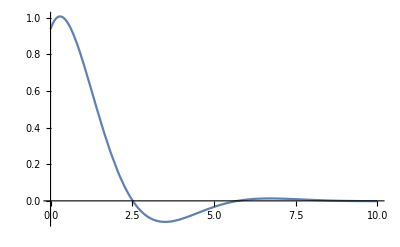

```mathematica
Plot[ustar1,{t,0,10},PlotRange->Full]
```

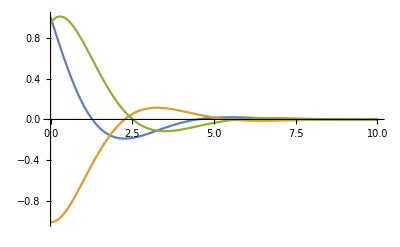

```mathematica
Plot[{xSol1,dxSol1,ustar1},{t,0,10},PlotRange->Full]
```

```mathematica
qSol=qMat/.{q1Sol[[1,1]],q2Sol[[1,1]]}
```

{{-p+p ω_n^4,0},{0,2 (p-p ω_n^2+2 p ζ^2 ω_n^2)}}

```mathematica
MatrixForm[qSol]
```

(-p+p ω_n^4 | 0
0 | 2 (p-p ω_n^2+2 p ζ^2 ω_n^2))

```mathematica
phi=FullSimplify[Transpose[xVec].qSol.xVec+p ustar^2]
```

{{ⅇ^(-2 t ζ ω_n) (2 (p+p (-1+2 ζ^2) ω_n^2) (Cosh[t √(-1+ζ^2) ω_n]+(Sinh[t √(-1+ζ^2) ω_n] (-ζ+ω_n))/(√(-1+ζ^2)))^2+p (-1+ω_n^4) (Cosh[t √(-1+ζ^2) ω_n]+(Sinh[t √(-1+ζ^2) ω_n] (-1+ζ ω_n))/(√(-1+ζ^2) ω_n))^2+p (2 ζ (-Cosh[t √(-1+ζ^2) ω_n]+(Sinh[t √(-1+ζ^2) ω_n] (ζ-ω_n))/(√(-1+ζ^2))) ω_n+(-1+ω_n^2) (Cosh[t √(-1+ζ^2) ω_n]+(Sinh[t √(-1+ζ^2) ω_n] (-1+ζ ω_n))/(√(-1+ζ^2) ω_n)))^2)}}

```mathematica
(*j=Integrate[phi,{t,0,tf}];*)
```

```mathematica
j=∫_0^tf phiⅆt
```

{{p (2+2 ω_n (ζ-ω_n+ζ ω_n^2)+1/((-1+ζ^2) ω_n)ⅇ^(-2 tf ζ ω_n) (ζ-ζ Cosh[2 tf √(-1+ζ^2) ω_n]+√(-1+ζ^2) Sinh[2 tf √(-1+ζ^2) ω_n]+ω_n (2 (-ζ^2+Cosh[2 tf √(-1+ζ^2) ω_n])+ω_n (2 (ζ-ζ^3 Cosh[2 tf √(-1+ζ^2) ω_n]+(-1+ζ^2)^(3/2) Sinh[2 tf √(-1+ζ^2) ω_n])+ω_n (-2 ζ^2+(-2+4 ζ^2) Cosh[2 tf √(-1+ζ^2) ω_n]+(ζ+(ζ-2 ζ^3) Cosh[2 tf √(-1+ζ^2) ω_n]+(1-2 ζ^2) √(-1+ζ^2) Sinh[2 tf √(-1+ζ^2) ω_n]) ω_n)))))}}

```mathematica
j1=j/.{Subscript[ω, n]->1.1892,ζ->0.5685,tf->10}
```

{{(2.43589+0. ⅈ) p}}

```mathematica
dxZero=Solve[dxSol==0,t];
```

```mathematica
tshift=FullSimplify[t/.dxZero[[2]]]
```

```mathematica
-ArcCosh[(-ζ+Subscript[ω, n])/(√(1-2 ζ Subscript[ω, n]+Subscript[ω, n]^2))]/(√(-1+ζ^2) Subscript[ω, n])
```

```mathematica
xshift=FullSimplify[xSol/.t->tshift]
```

ⅇ^((ζ ArcCosh[(-ζ+ω_n)/(√(1-2 ζ ω_n+ω_n^2))])/(√(-1+ζ^2))) ((-ζ+ω_n)/(√(1-2 ζ ω_n+ω_n^2))-((-1+ζ ω_n) (1+(-ζ+ω_n)/(√(1-2 ζ ω_n+ω_n^2))) √(-(ζ-ω_n+√(1-2 ζ ω_n+ω_n^2))/(-ζ+ω_n+√(1-2 ζ ω_n+ω_n^2))))/(√(-1+ζ^2) ω_n))

```mathematica
tshift1=Re[tshift]/.{Subscript[ω, n]->1.1892,ζ->0.5685}
```

-0.944904

```mathematica
Subscript[ω, d]=Subscript[ω, n] √(1-ζ^2);
```

```mathematica
θ=ArcCos[ζ];
```

```mathematica
Subscript[t, r]=Re[tshift+(π-θ)/Subscript[ω, d]]
```

Re[(π-ArcCos[ζ])/(√(1-ζ^2) ω_n)-ArcCosh[(-ζ+ω_n)/(√(1-2 ζ ω_n+ω_n^2))]/(√(-1+ζ^2) ω_n)]

```mathematica
Subscript[t, p]=Re[tshift+π/Subscript[ω, d]]
```

Re[π/(√(1-ζ^2) ω_n)-ArcCosh[(-ζ+ω_n)/(√(1-2 ζ ω_n+ω_n^2))]/(√(-1+ζ^2) ω_n)]

```mathematica
Subscript[t, r,1]=Subscript[t, r]/.{Subscript[ω, n]->1.1892,ζ->0.5685}
```

1.27875

```mathematica
Subscript[t, p,1]=Subscript[t, p]/.{Subscript[ω, n]->1.1892,ζ->0.5685}
```

2.26626

```mathematica
Subscript[t, s5]=Re[tshift-Log[0.05/xshift]/(ζ Subscript[ω, n])];
```

```mathematica
Subscript[t, s5,1]=Subscript[t, s5]/.{Subscript[ω, n]->1.1892,ζ->0.5685}
```

4.21939

```mathematica
Subscript[t, s2]=Re[tshift-Log[0.02/xshift]/(ζ Subscript[ω, n])];
```

```mathematica
Subscript[t, s2,1]=Subscript[t, s2]/.{Subscript[ω, n]->1.1892,ζ->0.5685}
```

5.57473

```mathematica
Solve[Subscript[t, r]==2,ζ]
```

Solve[Re[(π-ArcCos[ζ])/(√(1-ζ^2) ω_n)-ArcCosh[(-ζ+ω_n)/(√(1-2 ζ ω_n+ω_n^2))]/(√(-1+ζ^2) ω_n)]==2,ζ]

```mathematica
Eigenvalues[aMat-bVec.kTrn]
```

{-ζ ω_n-√(-ω_n^2+ζ^2 ω_n^2),-ζ ω_n+√(-ω_n^2+ζ^2 ω_n^2)}